# Plots Across Parameter Runs

## Data Selection

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
plotsDir= "kl_div_plots";
dataDir = "mlflow_data";
bcRateKHz = 28608.8064;
```

```mathematica
(*Set the name of the experiment.*)
experiments =FileNameTake/@(FileNames[All, dataDir]);
experimentName =.;
PopupMenu[Dynamic[experimentName],experiments]
```

```mathematica
(*Get the experiment directory and the names of all the runs in that directory.*)
experimentDir=FileNameJoin[{dataDir, experimentName}];
runDirs = FileNames[All, experimentDir];
runNames = FileNameTake/@runDirs;

(*Select which metric to plot.*)
availableMetrics = {"kl", "reco", "loss" ,"z_mean_squared_rate0.3", "loss_reco_full_rate0.3","loss_total_full_rate0.3", "loss_kl_full_rate0.3", "cap"};
desiredMetric=availableMetrics[[1]];
PopupMenu[Dynamic[desiredMetric, (desiredMetric=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"datasetSelection"}}])&
],availableMetrics]
desiredMetricPlotStyling = <|"kl"->"α × D_KL[𝒵 || 𝒩(0, 1)]", "reco"->"(1-α)×(𝒳 - 𝒳̂)^2", "loss"->"α × D_KL[𝒵 || 𝒩(0, 1)] + (1-α)×(𝒳 - 𝒳̂)^2", "z_mean_squared_rate0.3"->"TPR @ 10^-5 FPR (μ^2)", "loss_reco_full_rate0.3"->"TPR @ 10^-5 FPR (MSE)", "loss_total_full_rate0.3"->"TPR @ 10^-5 FPR (total)", "loss_kl_full_rate0.3"->"TPR @ 10^-5 FPR (KL)", "cap" -> "Approximation Capacity"|>;
```

```mathematica
datasets = Intersection[FileNameTake/@Flatten@Table[FileNames[All, runDirs[[i]]],{i, 1, Length@runDirs}]];
datasets = If[desiredMetric == "cap", Select[datasets, StringContainsQ[desiredMetric]],Select[datasets, StringContainsQ[desiredMetric <> "."]]];
desiredDataset=datasets[[2]];
PopupMenu[Dynamic[desiredDataset, (desiredDataset=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"labels","importData","plotGrid"}}])&
],datasets]
```

## Metadata

```mathematica
(*Extract parameters from run names. Will be used as labels for the plots.*)
processRunName[runName_] := (
name = {};
splitRunName = StringSplit[runName,"_"];
lrName = Select[splitRunName, StringContainsQ["lr"]];
alphaName =Select[splitRunName, StringContainsQ["alpha"]];
name =Append[name, "ℓ = "<>Flatten@StringCases[lrName,NumberString] <> ", " <> "α = "<>Flatten@StringCases[alphaName,NumberString]];
name
)
runLabels =processRunName/@runNames;
Style["List of the runs that will be plotted: ", "Subsection"]
Framed[Pane[Column[runLabels], {200, 150}, Scrollbars->True]]
completeRunLabels = {{"ℓ = 0.0001, α = 0.1"},{"ℓ = 0.0001, α = 0.2"},{"ℓ = 0.0001, α = 0.3"},{"ℓ = 0.0001, α = 0.4"},{"ℓ = 0.0001, α = 0.5"},{"ℓ = 0.0001, α = 0.6"},{"ℓ = 0.0001, α = 0.7"},{"ℓ = 0.0001, α = 0.8"},{"ℓ = 0.0001, α = 0.9"},{"ℓ = 0.00025, α = 0.1"},{"ℓ = 0.00025, α = 0.2"},{"ℓ = 0.00025, α = 0.3"},{"ℓ = 0.00025, α = 0.4"},{"ℓ = 0.00025, α = 0.5"},{"ℓ = 0.00025, α = 0.6"},{"ℓ = 0.00025, α = 0.7"},{"ℓ = 0.00025, α = 0.8"},{"ℓ = 0.00025, α = 0.9"},{"ℓ = 0.0005, α = 0.1"},{"ℓ = 0.0005, α = 0.2"},{"ℓ = 0.0005, α = 0.3"},{"ℓ = 0.0005, α = 0.4"},{"ℓ = 0.0005, α = 0.5"},{"ℓ = 0.0005, α = 0.6"},{"ℓ = 0.0005, α = 0.7"},{"ℓ = 0.0005, α = 0.8"},{"ℓ = 0.0005, α = 0.9"},{"ℓ = 0.00075, α = 0.1"},{"ℓ = 0.00075, α = 0.2"},{"ℓ = 0.00075, α = 0.3"},{"ℓ = 0.00075, α = 0.4"},{"ℓ = 0.00075, α = 0.5"},{"ℓ = 0.00075, α = 0.6"},{"ℓ = 0.00075, α = 0.7"},{"ℓ = 0.00075, α = 0.8"},{"ℓ = 0.00075, α = 0.9"},{"ℓ = 0.001, α = 0.1"},{"ℓ = 0.001, α = 0.2"},{"ℓ = 0.001, α = 0.3"},{"ℓ = 0.001, α = 0.4"},{"ℓ = 0.001, α = 0.5"},{"ℓ = 0.001, α = 0.6"},{"ℓ = 0.001, α = 0.7"},{"ℓ = 0.001, α = 0.8"},{"ℓ = 0.001, α = 0.9"}};
```

List of the runs that will be plotted:

{ℓ = 0.0001, α = 0.2}
{ℓ = 0.0001, α = 0.6}
{ℓ = 0.0001, α = 0.8}
{ℓ = 0.001, α = 0.2}
{ℓ = 0.001, α = 0.6}
{ℓ = 0.001, α = 0.8}

## Import Data

```mathematica
(*Get the data to plot from all the runs inside the experiment.*)
datasetPaths = Select[FileNames[All, runDirs],StringContainsQ[desiredDataset]];
plotData = AssociationThread[runLabels,BinaryReadList[#, "Real32"] & /@ datasetPaths];
(*1. Flatten your full list of desired labels*)
labelsWanted=completeRunLabels;

(*2. Which of those are absent from plotData?*)
missingLabels=Complement[labelsWanted,Keys@plotData];

(*3. Figure out the target vector length*)
vecLen=First@Commonest[Length/@Values@plotData];  (*robust if a few differ*)

(*4. Build zero-vectors for the missing keys*)
zerosForMissing=AssociationMap[ConstantArray[0.,vecLen]&,missingLabels];

(*5. Merge them in*)
plotData=Join[plotData,zerosForMissing];
plotData // Dimensions

Clear[interpIndeterminate];
interpIndeterminate[v_List]:=Module[{n=Length[v],good,bad,left,right,f,fill},good=Select[Range[n],NumericQ[v[[#]]]&];
bad=Complement[Range[n],good];
If[bad==={},Return[v]];(*nothing to do*)(*If we can't interpolate,just freeze at the only numeric value or zero*)If[Length[good]<2,Return@Replace[v,Indeterminate->If[good==={},0.,v[[First@good]]]]];
{left,right}={First[good],Last[good]};
f=Interpolation[Thread[good->v[[good]]],InterpolationOrder->1];
fill[i_]/;i<left:=v[[left]];(*hold left edge*)fill[i_]/;i>right:=v[[right]];(*hold right edge*)fill[i_]:=f[i];(*interior:interpolate*)ReplacePart[v,Thread[bad->(fill/@bad)]]];

plotData=Map[interpIndeterminate,plotData];
cleanVec[v_List]:=v/. r_Rule:>r[[2]];

plotData=Map[cleanVec,plotData];

(*Restrict values to be between 0 and 1, for better plotting visibility if the data is kl divergence related.*)
If[desiredMetric == "kl",plotData =Map[Clip[#,{0,2}]&, plotData]];
If[desiredMetric == "loss",plotData =Map[Clip[#,{0,4}]&, plotData]];
If[StringContainsQ[desiredMetric, "rate"], plotData = plotData/bcRateKHz];
```

{45}

```mathematica
Style["Plotting data for " <> desiredDataset, "Title"]
```

Plotting data for cap_background0.dat

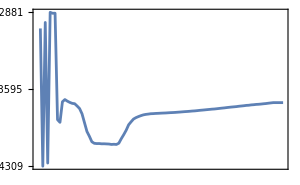
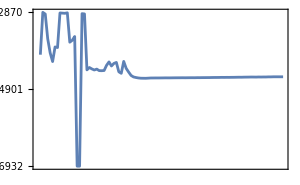
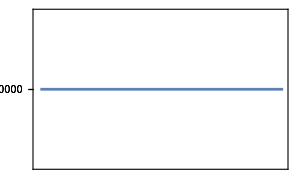
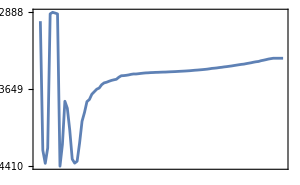
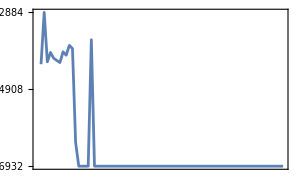
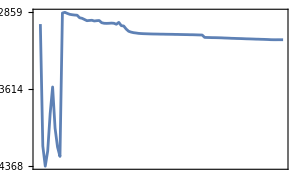
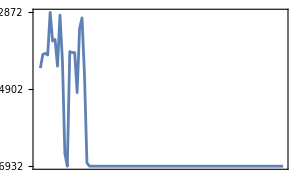
|  | ℓ = 0.0001 | ℓ = 0.001 | ℓ = 0.00025 | ℓ = 0.0005 | ℓ = 0.00075
 α = 0.2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 α = 0.6 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 α = 0.8 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 α = 0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 α = 0.3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 α = 0.4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 α = 0.5 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 α = 0.7 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 α = 0.9 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Epochs ∈ [0, 100]cap_background0

```mathematica
(*---helper to normalize keys to plain strings---*)
keyString[k_]:=If[ListQ[k],First[k],k];

(*Plotting code.*)
makePlot[row_]:=ListLinePlot[
row,
PlotStyle->{Medium},
Axes->False,
Frame->True,
PlotRange->{All, {Min[row], Max[row]}},
PlotRangePadding->{0, Scaled[.2]};
FrameTicks->{{{{Min[row],NumberForm[N[Min[row]],{5,4}]},{(Min[row]+(Max[row] - Min[row])/2),NumberForm[N[Min[row]+(Max[row] - Min[row])/2],{5,4}]},{Max[row],NumberForm[N[Max[row]],{5,4}]}},None},{None,None}},
ImageSize->{300, 200}
]
(*2. Build plots in current key order*)
plots=makePlot/@plotData;

(*3. Extract parameter strings from the keys*)

keysStr=Keys[plotData];
learningRates=DeleteDuplicates[(StringSplit[#[[1]],","][[1]]&/@keysStr)];
alphas=DeleteDuplicates[(StringSplit[#[[1]],","][[2]]&/@keysStr)];

(*4. Put plots into a matrix:group by learning rate, varying alpha.*)

(*Create an index:{η,α}->position in 'plots'*)
keyIndex=AssociationThread[keysStr->Range@Length@plots];
indexOf[η_,α_]:=Lookup[keyIndex,{{StringJoin[η,",",α]}}/. WhitespaceCharacter..->" ",Missing["NotAvailable"]];

(*Build the grid of plots using the index*)
grid=Table[With[{pos=indexOf[lr,a]},If[MissingQ[pos],Graphics[{}],plots[[pos]][[1]]]],{a,alphas},{lr,learningRates}];

(*5. Label rows/cols and build the final grid exactly like you did*)
rowsWithLabels=MapThread[Prepend,{grid,alphas}];
colLabels=learningRates;
fullGrid=Prepend[rowsWithLabels,Prepend[colLabels,""]];

fullGridWithAxes=Grid[{{"",Grid[fullGrid,Spacings->{1,1},Alignment->Center]},{"",Style["Epochs ∈ [0, 100]",FontWeight->"SemiBold",24,Gray]}},Spacings->{1,2}];

yLabel=Style[Rotate[FileBaseName@desiredDataset,90 Degree],FontWeight->"SemiBold",24,Gray];

Labeled[fullGridWithAxes,yLabel,Left,LabelStyle->{FontSize->24},Spacings->{1,2}]
```

```mathematica
Export["run_grids/" <>FileBaseName@desiredDataset <> ".png",%]
```

run_grids/cap_background1.png

# Overall Plot

```mathematica
processDatasetNames[datasetName_] := StringReplace[FileBaseName@StringSplit[datasetName, "/"][[-1]], RegularExpression["^(val_)?|(_loss.*|_rate.*|_cap.*)"]-> ""]
datasetPlotStyling=<|
"train"->"ZeroBias_train",
"ggXToJpsiJpsiTo2Mu2E_m7_pseudoscalar"->"gg → X_(7 GeV) → J/ψ J/ψ → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m14_pseudoscalar"->"gg → X_(14 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m18_pseudoscalar"->"gg → X_(18 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"ggXToYYTo2Mu2E_m26_pseudoscalar"->"gg → X_(26 GeV) → YY → (μ⁺μ⁻)(e⁺e⁻)",
"GluGluHToBB_M-125"-> "gg → H(125 GeV) → bb̄",
"GluGluHToGG_M-125"-> "gg → H(125 GeV) → gg",
"GluGluHToGG_M-90"->"gg → H(90 GeV) → gg", 
"GluGluHToTauTau_M-125"-> "gg → H(125 GeV) → τ^+τ^-",
"GluGlutoHHto2B2WtoLNu2Q_kl-1p00_kt-1p00_c2-0p00"-> "gg → HH → bb̄W^+W^- → (l^±ν)(qq̄')",
"HHHto4B2Tau_c3-0_d4-0" -> "HHH → bb̄bb̄τ^+τ^-",
"HHHTo6B_c3_0_d4_0"->"HHH → 6b",
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-100000mm"-> "H (10^3 GeV) → LL (10^3 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-12_CTau-900mm" -> "H (125 GeV) → LL (900 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-25_CTau-1500mm" ->"H (125 GeV) → LL (1500 mm) → 4b",
"HTo2LongLivedTo4b_MH-125_MFF-50_CTau-3000mm" -> "H (125 GeV) → LL (3000 mm) → 4b",
"haa-4b-ma15"->"H → AA → 4b", 
"VBFHto2B_M-125"->"VV → H → bb̄", 
"HTo2LongLivedTo4b_MH-1000_MFF-450_CTau-10000mm" -> "H (10^3 GeV) → 2LL (10^4 mm) → 4b", 
"main_val"->"ZeroBias",
"SingleNeutrino_E-10-gun" -> "Zero Bias Simulation E-10",
"SingleNeutrino_Pt-2To20-gun" -> "Zero Bias Simulation p_T ∈ [2, 20]",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT-60" -> "higgsino 1",
"SMS-Higgsino_mN2-170_mC1-160_mN1-150_HT60" ->"higgsino 2",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_1" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-1200_2" -> "gg → bb̄H(1200 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_1" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-120_2" -> "gg → bb̄H(120 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_1" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-350_2" -> "gg → bb̄H(350 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_1" -> "gg → bb̄H(600 GeV) → bb̄",
"SUSYGluGluToBBHToBB_NarrowWidth_M-600_2"-> "gg → bb̄H(600 GeV) → bb̄",
"ttHto2B_M-125" -> "tt̄ → H(125 GeV) → bb̄",
"ttHto2C_M-125" -> "tt̄ → H(125 GeV) → cc̄",
"VBFHToCC_M-125"->"VV → H → cc̄",
"VBFHToInvisible_M-125"->"VV → H → invis",
"VBFHToTauTau_M125"->"VV → H → τ^+τ^-",
"Wlnu" -> "W^± → l^±ν_l",
"WToTauTo3Mu" -> "W^± → τ^± → μ^±μ^+μ^-",
"WToTauToMuMuMu" -> "W^± → τ^± → μ^±μ^+μ^-",
"cap_background1"->"Zero Bias Simulation p_T ∈ [2, 20]",
"cap_background0"->"Single Neutrino E-10 Gun",
"cap_baseline"->"Zero Bias Validation"
|>;
processDatasetNames@desiredDataset
stylizedDesiredDataset = datasetPlotStyling[processDatasetNames@desiredDataset]

(*Select which datasets to plot.*)
(*plottedDatasets =  {{"ℓ = 0.0001, α = 0.2"},{"ℓ = 0.0001, α = 0.6"},{"ℓ = 0.0001, α = 0.8"}};*)
plottedDatasets =  {{"ℓ = 0.001, α = 0.2"},{"ℓ = 0.001, α = 0.6"},{"ℓ = 0.001, α = 0.8"}};
(*plottedDatasets =  {{"ℓ = 0.001, α = 0.6"},{"ℓ = 0.0005, α = 0.6"},{"ℓ = 0.0001, α = 0.6"}};*)
data = KeyTake[plotData,plottedDatasets];
data = KeyValueMap[Function[{key,mat},key->Module[{nelements=Dimensions[mat][[1]]},Table[{i,mat[[i]]},{i, nelements}]]],data];

(*Color function for selected lines*)
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
colorFunc=Function[i,RGBColor[hexColors[[Mod[i-1,Length[hexColors]]+1]]]];

(*Extract and scale series*)
series=Values[data];

(*Determine scaling for y-values:two significant figures*)
allYRaw=Flatten[series[[All,All,2]]];
scaleExp=Floor[Log10[Max[Abs[allYRaw]]]];
scaleFactor=10^scaleExp;

scaledSeries=Map[{#[[1]],#[[2]]/scaleFactor}&,series,{2}];

(*Legend labels*)
labelsKeys=Style[#[[1]],FontSize->25]&/@(plottedDatasets);

(*X-axis ticks:major every 5,minor every 1*)
numCols=Length@First@series;
majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
majorPositions=Range[1,numCols,5];
majorTicks=Table[{i,i-1,{majorLen,0}},{i,majorPositions}];
minorPositions=Complement[Range[1,numCols],majorPositions];
minorTicks=Table[{i,"",{minorLen,0}},{i,minorPositions}];
xTicks=Join[majorTicks,minorTicks];
xTicksUpper=xTicks/. {v_,_,len_}:>{v,"",len};

(*Y-axis ticks:5 intervals on scaled data,formatted to 2 significant figures*)
allY=Flatten[scaledSeries[[All,All,2]]];
yMin=Min[allY];
yMax=Max[allY];
yStep=(yMax-yMin)/5;
(*Major Y-ticks*)
majorPositionsY=Table[yMin+i*yStep,{i,0,5}];
majorTicksY=Table[{pos,NumberForm[pos,{3,2}],{majorLen,0}},{pos,majorPositionsY}];
(*Minor Y-ticks:5 between majors*)
minorTicksY=Flatten[Table[Table[{majorPositionsY[[k]]+j*(yStep/6),"",{minorLen,0}},{j,1,5}],{k,1,Length[majorPositionsY]-1}],1];
(*Combined Y-ticks*)
yTicks=Join[majorTicksY,minorTicksY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};

legendY=0.84;          (*how low the legend sits (0=bottom,1=top)*)
ruleY=legendY+0.1;(*y of the horizontal line,tweak as needed*)

legendPosition = {Scaled[{0.83,legendY}], Scaled[{0.98,1.01}],Scaled[{0.65,ruleY}], Scaled[{0.99,ruleY}]};
shift={-0.03,-0.1};  
legendPosition=legendPosition/. Scaled[p_]:>Scaled[p+shift];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
leftPad=150;   (*room for y ticks+your CMS tag*)
topPad=70;    (*room above frame*)
tevText = Row[{Style["14 TeV",FontFamily->"TeX Gyre Heros",24],""}];

(*Plot*)
plt =ListLinePlot[
scaledSeries,
Joined->True,
Axes->False,
Frame->True,
PlotRange->All,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksUpper}},FrameLabel->{Style["Epoch",Black,FontSize->30,FontFamily->"TeX Gyre Heros"],Style[Row[{desiredMetricPlotStyling[desiredMetric],If[scaleExp!=0," ×",""],If[scaleExp!=0,Superscript[10,scaleExp]], ""}],Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},PlotStyle->(colorFunc/@Range[Length@series]),
PlotLegends->Placed[SwatchLegend[labelsKeys,LegendMarkerSize->15,LabelStyle->Directive[Black,FontSize->18,FontFamily->"TeX Gyre Heros"]],legendPosition[[1]]],
LabelStyle->Directive[Black,FontSize->28,FontFamily->"TeX Gyre Heros"],
FrameTicksStyle->Directive[AbsoluteThickness[2]],
Epilog->{
Text[Row[{Style[stylizedDesiredDataset,FontFamily->"TeX Gyre Heros",Italic,FontSize->28]}],legendPosition[[2]],{Right,Top}],
{GrayLevel[.2],AbsoluteThickness[3],Line[{legendPosition[[3]],legendPosition[[4]]}]},
Nothing
},
PlotRangePadding->{{Scaled[0.01],Scaled[0.017]},{Scaled[0.04],Scaled[0.04]}},
ImageSize->1300,
AspectRatio->0.5
];
outer=Graphics[{Inset[plt,Scaled[{0,0}],{Left,Bottom},Scaled[1]],Inset[cmsText,Scaled[{0.095,0.93}],{Left,Bottom},Scaled[1]],Inset[tevText,Scaled[{0.83,0.94}],{Left,Bottom},Scaled[1]]},PlotRange->{{0,1},{0,1}}, AspectRatio->0.5, ImageSize->1300]
```

cap_background0

Single Neutrino E-10 Gun

-Graphics-

```mathematica
Export["final_presentation_plots/" <>"parameter_explore_" <> desiredMetric <>"_" <> processDatasetNames@desiredDataset <>"_lr0.001.pdf",outer]
```

final_presentation_plots/parameter_explore_cap_cap_background0_lr0.001.pdf

```mathematica
Export["final_presentation_plots/" <>"parameter_explore_" <> desiredMetric <>"_" <> processDatasetNames@desiredDataset <>"_lr0.0001.pdf",outer]
```

final_presentation_plots/parameter_explore_cap_cap_background0_lr0.0001.pdf

```mathematica
Export["final_presentation_plots/" <>"parameter_explore_" <> desiredMetric <>"_" <> processDatasetNames@desiredDataset <>"_alpha0.6.pdf",outer]
```

final_presentation_plots/parameter_explore_loss_kl_full_rate0.3_haa-4b-ma15_alpha0.6.pdf